Hyperbolic Trigonometric Functions

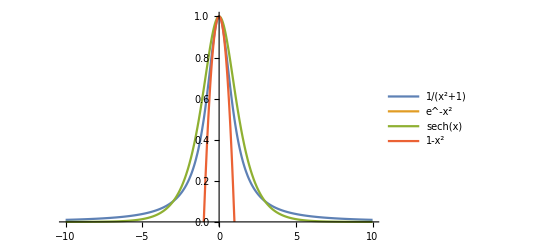

```mathematica
Plot[{1/(x^2+ 1), e^(-x^2),Sech[x],1-x^2},{x,-10,10},PlotRange->{0,1},PlotLegends->"Expressions"]
```

Vector Fields:

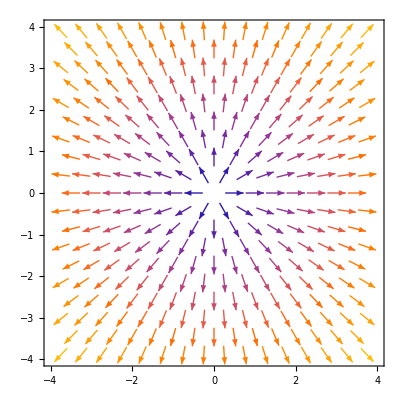

```mathematica
VectorPlot[{x,y},{x,-4,4},{y,-4,4}]
```

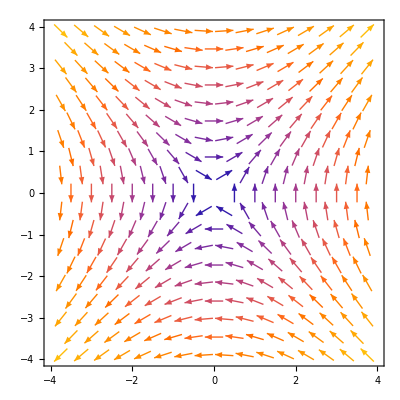

```mathematica
VectorPlot[{y,x},{x,-4,4},{y,-4,4}]
```

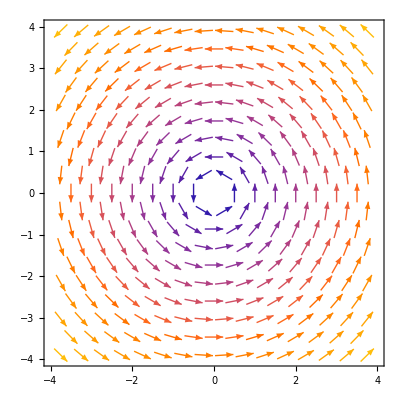

```mathematica
VectorPlot[{-y,x},{x,-4,4},{y,-4,4}]
```

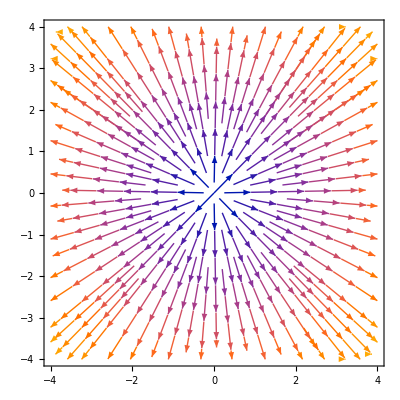

```mathematica
StreamPlot[{x,y},{x,-4,4},{y,-4,4}]
```

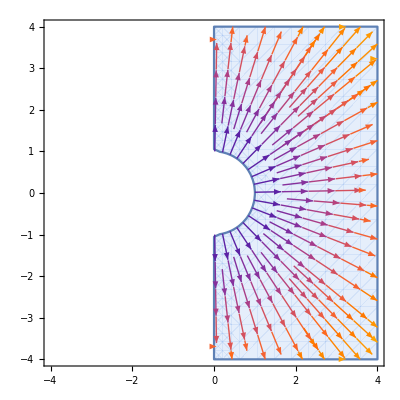

```mathematica
StreamPlot[{x,y},{x,-4,4},{y,-4,4}, RegionFunction-> Function[{x,y,vx,vy,n} ,n > 1&& vx > 0
 ]]
```

```mathematica
VectorPlot3D[{x,y,z},{x,-4,4},{y,-4,4},{z,-4,4},VectorScaling -> 0.06]
```

-Graphics3D-

```mathematica
VectorPlot3D[{-y,x,z},{x,-4,4},{y,-4,4},{z,-4,4},VectorScaling -> 0.06]
```

-Graphics3D-

# Field lines and Equipotential Surfaces

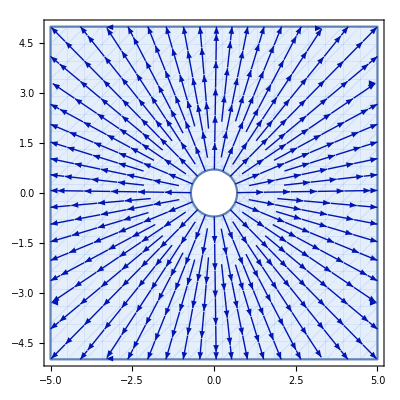

```mathematica
StreamPlot[{ x/(√((x^2+y^2)^3)), y/(√((x^2+y^2)^3))},{x,-5,5},{y,-5,5}, RegionFunction -> Function[{x,y,vx,vy,n}, n<2]]
```

## Dipole Example

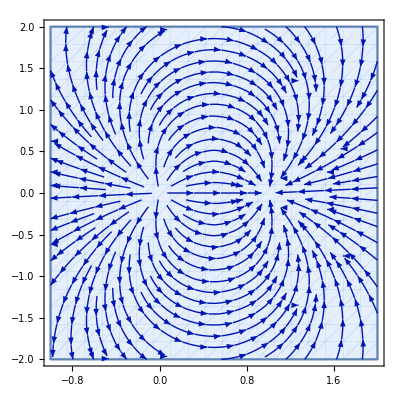

```mathematica
fieldLines = StreamPlot[{x/r^3-(x-1)/r1^3,y/r^3-y/r1^3}/.r->√(x^2+y^2)/.r1->√((x-1)^2+y^2),{x,-1,2},{y,-2,2},RegionFunction->Function[{x,y,vx,vy,n},n<200]]
```

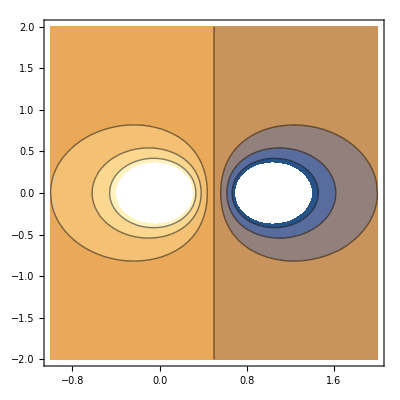

```mathematica
equiPotential = ContourPlot[{1/r-1/r1}/.r->√(x^2+y^2)/.r1->√((x-1)^2+y^2),{x,-1,2},{y,-2,2}]
```

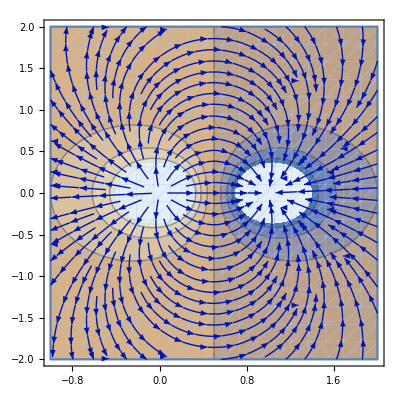

```mathematica
Show[equiPotential, fieldLines]
```